```mathematica
C0:=12/Pi^2;
N[C0]
```

1.21585

```mathematica
(* probability distribution object based on the analytic density function: *)
(* not helpful since even computing the mean of the distribution takes forever. *)
z2Dist:=ProbabilityDistribution[densityFctSL[t,1.0],{t,0,Infinity}];
```

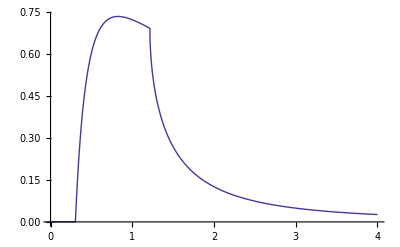

```mathematica
Plot[t*densityFctSL[t,1.0],{t,0,4},Exclusions->None]
```

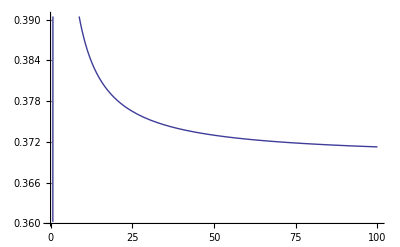

```mathematica
(* one can see that computing the third moment is going to be complicated. *)
(* the decay of the function is very slow, probably not even going to zero. *)
Plot[t^3*densityFctSL[t,1.0],{t,0,100},Exclusions->None]
```

```mathematica
(* in fact it really doesn't go to zero, but to a positive value. *)
(* the third moment therefore doesn't exist! *)
h[t_]:=Log[2/(1+Sqrt[1-12/(Pi^2*t)])];
{Limit[x*h[x],x->Infinity],Limit[h[x],x->Infinity],Limit[h[x]/x,x->Infinity]}
```

{3/π^2,0,0}

```mathematica
Series[h[1/t],{t,0,3}]
```

(3 t)/π^2+(27 t^2)/(2 π^4)+(90 t^3)/π^6+O[t]^4

```mathematica
h[1/t]
```

Log[2/(1+√(1-(12 t)/π^2))]

```mathematica
h1[t_]=Integrate[t*densityFctSL[t,1],t];
h2[t_]=Integrate[t^2*densityFctSL[t,1],t];
h3[t_]=Integrate[t^3*densityFctSL[t,1],t];
```

```mathematica
N[h2[12/Pi^2]]
```

0.412298

```mathematica
Map[Limit[#[t],t->Infinity]&,{h3,h2,h1,h}]
```

$Aborted

```mathematica
N[3/Pi^2]
```

0.303964

```mathematica
h1[t]
```

Piecewise[{{0, t≤3/π^2}, {(3 Log[(π^2 t)/3]^2)/π^2, 3/π^2<t≤12/π^2}, {(3 Log[4]^2)/π^2-(2 π^2+6 Log[12]^2+6 ⅈ π (Log[3]-2 Log[π])-3 Log[12/π^2] (Log[108]-2 Log[π])-12 Log[12] Log[π])/π^2+(12 (Log[(2 π)/(π+√(π^2-12/t))] Log[t]+1/12 (-3 Log[t]^2+(12 ⅈ √(π^2-12/t) √t (ArcSin[(π √t)/(2 √3)]^2-2 ⅈ ArcSin[(π √t)/(2 √3)] Log[1-ⅇ^(-2 ⅈ ArcSin[(π √t)/(2 √3)])]+Log[t] Log[(ⅈ π √t+√(12-π^2 t))/(2 √3)]+PolyLog[2,ⅇ^(-2 ⅈ ArcSin[(π √t)/(2 √3)])]))/(√(12-π^2 t)))))/π^2, True}}]

```mathematica
Map[h2,{1000.0,5000.0,10000.0,50000.0}]
```

{3.17766+0. ⅈ,3.77261+0. ⅈ,4.02879+0. ⅈ,4.62362+0. ⅈ}

```mathematica
Limit[h2[t],t->Infinity]
```

∞

```mathematica
Limit[h[x],x->Infinity]
```

0

```mathematica
NIntegrate[t*densityFctSL[t,1.0],{t,0,C0},
MaxRecursion->18,Method->"LocalAdaptive"]
```

0.584161

```mathematica
NIntegrate[t*densityFctSL[t,1.0],{t,C0,Infinity},
MaxRecursion->18,Method->"LocalAdaptive"]
```

0.415839

```mathematica
Integrate[t^2*densityFctSL[t,1.0],{t,0,C0}]
```

0.470317

```mathematica
(* even for the second moment integrating the tail is a hopeless case. *)
Map[NIntegrate[t^2*densityFctSL[t,1.0],{t,C0,Infinity},Method->#]&,
{"LocalAdaptive","GlobalAdaptive","DoubleExponential","MonteCarlo","AdaptiveMonteCarlo"}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.99999790161194879179130405268826059322953267499536864978189960942}. NIntegrate obtained 50.8661 and 0.0248434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.13224×10^28}. NIntegrate obtained 8587.65 and 7300.6 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in t in the region {{1.21585, ∞}}. NIntegrate obtained 13.9012 and 0.00510152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 4.34144 and 0.360624 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in t near {t} = {0.998767}. NIntegrate obtained 5.94549 and 1.3679 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{55.8526,8587.65,13.9012,4.34144,5.94549}

```mathematica
(* in line with the other moment computation we just rely on a large list *)
data[Z2Lattice]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/z2lat.ang"];
```

```mathematica
Length[data[Z2Lattice]]
```

4834354

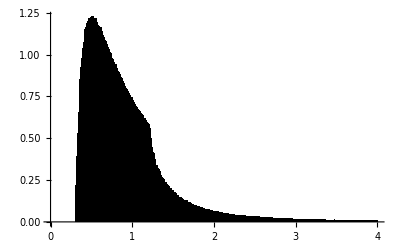

```mathematica
z2hist=RadialHistoPDF[Z2Lattice]
```

```mathematica
(* this looks a lot better than the integrated values *)
ComputeStats[data[Z2Lattice]]
```

{{1.0002,2.65737,228.056,142430.},0.304195}

```mathematica
N[3/Pi^2]
```

0.303964

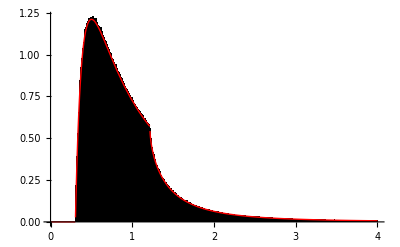

```mathematica
Show[z2hist,Plot[densityFctSL[x,1.0],
{x,0,histoParams[[1]]},PlotStyle->Red]]
```